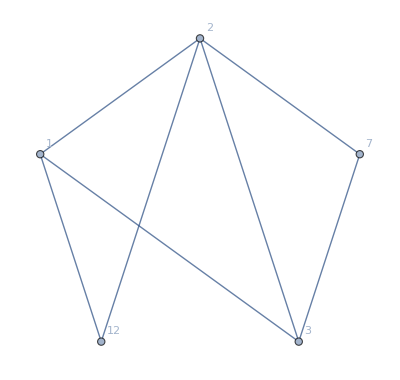
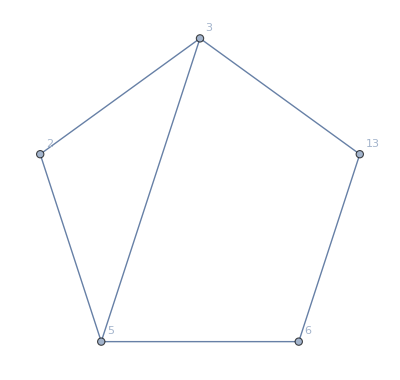
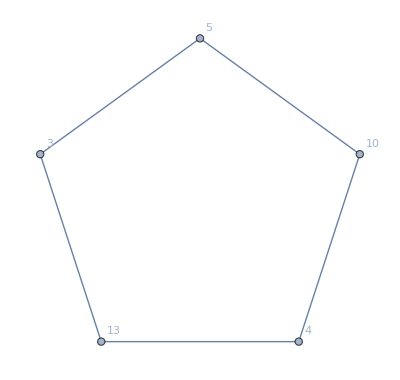
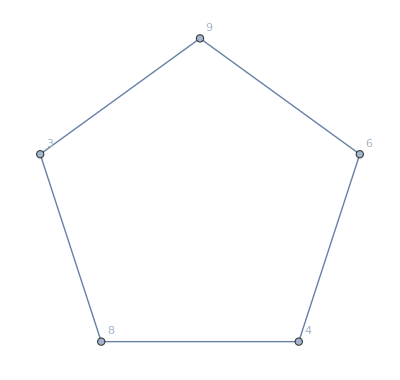
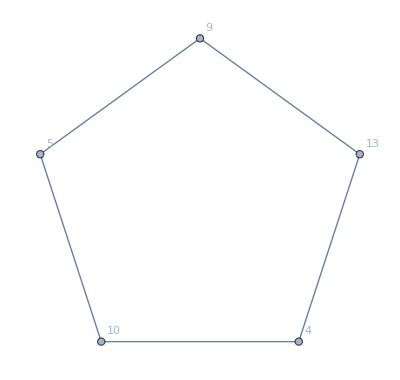
{{{1,2,3,12,7},-Graphics-,7},{{2,3,5,13,6},-Graphics-,6},{{3,5,13,4,10},-Graphics-,5},{{3,9,8,4,6},-Graphics-,5},{{5,9,13,4,10},-Graphics-,5}}

```mathematica
With[{k=10087},
Block[{g=ReadGrof[k], adj},
Table[
adj=AdjacencyList[g,v];
With[{h=Subgraph[g,adj]},

{adj,Graph[h,GraphLayout->"CircularEmbedding",VertexLabels->"Name"],EdgeCount[h]}
]
,{v,Select[VertexList[g],VertexDegree[g,#]==5&]}
]

]
]
```

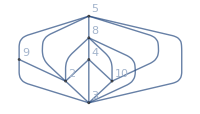
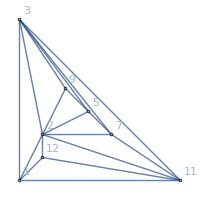
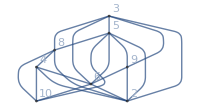
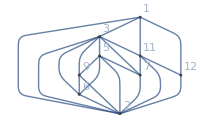
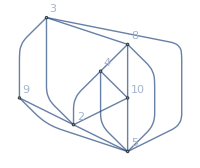
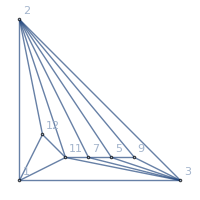
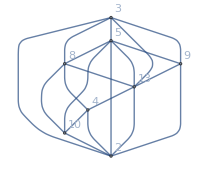
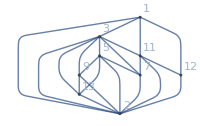
-Graphics-{(-3+x)^2 (-2+x) (13-7 x+x^2),24} | -Graphics-{(-3+x)^5 (-2+x),24}
-Graphics-{(-4+x) (-3+x)^2 (-2+x) (15-7 x+x^2),0} | -Graphics-{(-4+x) (-3+x)^5 (-2+x),0}
-Graphics-{(-3+x)^2 (-2+x) (10-6 x+x^2),48} | -Graphics-{(-3+x)^5 (-2+x),24}
-Graphics-{(-4+x) (-3+x)^2 (-2+x) (15-7 x+x^2),0} | -Graphics-{(-4+x) (-3+x)^5 (-2+x),0}
-Graphics-{(-4+x) (-3+x)^2 (-2+x)^2,0} | -Graphics-{(-3+x)^5 (-2+x),24}
-Graphics-{(-4+x) (-3+x)^2 (-2+x) (13-7 x+x^2),0} | -Graphics-{(-4+x) (-3+x)^5 (-2+x),0}
-Graphics-{(-4+x) (-3+x)^2 (-2+x) (10-6 x+x^2),0} | -Graphics-{(-4+x) (-3+x)^5 (-2+x),0}
-Graphics-{(-5+x) (-4+x) (-3+x)^2 (-2+x) (15-7 x+x^2),0} | -Graphics-{(-5+x) (-4+x) (-3+x)^5 (-2+x),0}6

```mathematica
With [{g=ReadGrof[10087],border={2,3,5,13,6}},
Labeled[TableForm[Map[{#[[2]],#[[3]]}&,ZykovDecomposition23[g,border]]],Style[EdgeCount[Subgraph[g,border]],Red,36],Top]
]
```

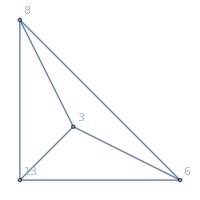
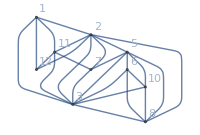
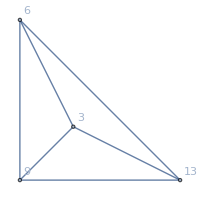
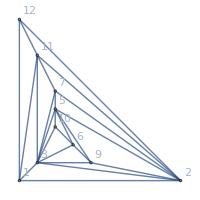
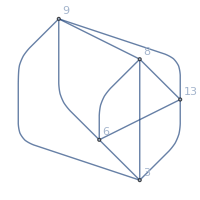
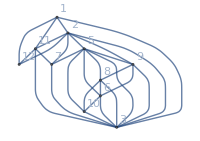
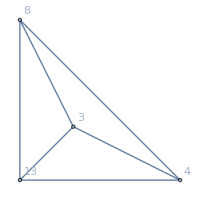
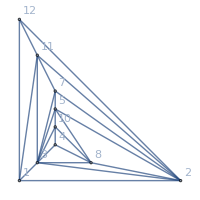
-Graphics-{(-3+x) (-2+x),24} | -Graphics-{(-4+x) (-3+x)^6 (-2+x),0}
-Graphics-{(-3+x) (-2+x),24} | -Graphics-{(-3+x)^7 (-2+x),24}
-Graphics-{(-4+x) (-3+x) (-2+x),0} | -Graphics-{(-4+x)^2 (-3+x)^6 (-2+x),0}
-Graphics-{(-3+x) (-2+x),24} | -Graphics-{(-3+x)^7 (-2+x),24}
-Graphics-{(-3+x) (-2+x),24} | -Graphics-{(-4+x) (-3+x)^6 (-2+x),0}
-Graphics-{(-4+x) (-3+x) (-2+x),0} | -Graphics-{(-3+x)^6 (-2+x) (13-7 x+x^2),24}
-Graphics-{(-4+x) (-3+x) (-2+x),0} | -Graphics-{(-3+x)^6 (-2+x) (13-7 x+x^2),24}
-Graphics-{(-3+x) (-2+x),24} | -Graphics-{(-3+x)^7 (-2+x),24}
-Graphics-{(-4+x) (-3+x) (-2+x),0} | -Graphics-{(-4+x)^2 (-3+x)^6 (-2+x),0}
-Graphics-{(-4+x) (-3+x) (-2+x),0} | -Graphics-{(-3+x)^6 (-2+x) (10-6 x+x^2),48}
-Graphics-{(-5+x) (-4+x) (-3+x) (-2+x),0} | -Graphics-{(-4+x) (-3+x)^6 (-2+x) (17-8 x+x^2),0}5

```mathematica
With [{g=ReadGrof[10087],border={3,9,8,4,6}},
Labeled[TableForm[Map[{#[[2]],#[[3]]}&,ZykovDecomposition23[g,border]]],Style[EdgeCount[Subgraph[g,border]],Red,36],Top]
]
```

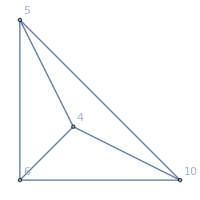
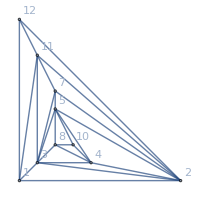
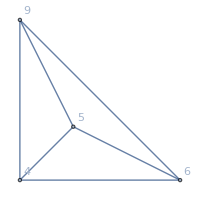
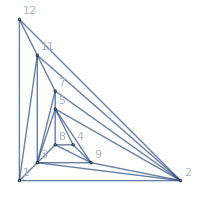
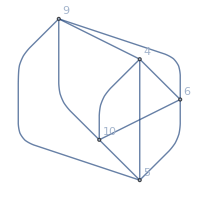
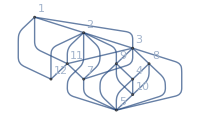
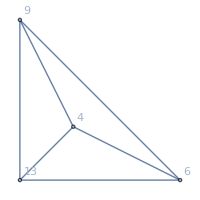
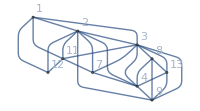
-Graphics-{(-3+x) (-2+x),24} | -Graphics-{(-3+x)^7 (-2+x),24}
-Graphics-{(-3+x) (-2+x),24} | -Graphics-{(-3+x)^7 (-2+x),24}
-Graphics-{(-4+x) (-3+x) (-2+x),0} | -Graphics-{(-3+x)^6 (-2+x) (10-6 x+x^2),48}
-Graphics-{(-3+x) (-2+x),24} | -Graphics-{(-4+x) (-3+x)^6 (-2+x),0}
-Graphics-{(-3+x) (-2+x),24} | -Graphics-{(-3+x)^7 (-2+x),24}
-Graphics-{(-4+x) (-3+x) (-2+x),0} | -Graphics-{(-3+x)^6 (-2+x) (13-7 x+x^2),24}
-Graphics-{(-3+x) (-2+x),24} | -Graphics-{(-4+x) (-3+x)^6 (-2+x),0}
-Graphics-{(-4+x) (-3+x) (-2+x),0} | -Graphics-{(-4+x)^2 (-3+x)^6 (-2+x),0}
-Graphics-{(-4+x) (-3+x) (-2+x),0} | -Graphics-{(-4+x)^2 (-3+x)^6 (-2+x),0}
-Graphics-{(-4+x) (-3+x) (-2+x),0} | -Graphics-{(-3+x)^6 (-2+x) (13-7 x+x^2),24}
-Graphics-{(-5+x) (-4+x) (-3+x) (-2+x),0} | -Graphics-{(-4+x) (-3+x)^6 (-2+x) (17-8 x+x^2),0}5

```mathematica
With [{g=ReadGrof[10087],border={5,9,13,4,10}},
Labeled[TableForm[Map[{#[[2]],#[[3]]}&,ZykovDecomposition23[g,border]]],Style[EdgeCount[Subgraph[g,border]],Red,36],Top]
]
```

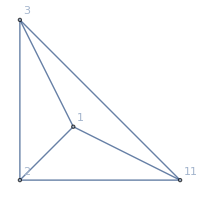
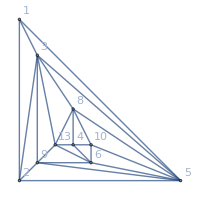
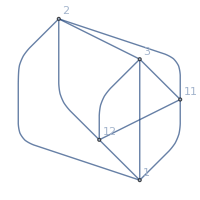
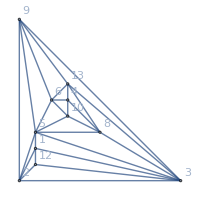
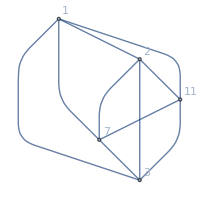
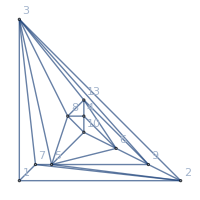
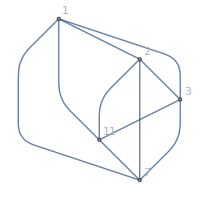
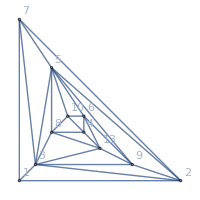
-Graphics-{(-3+x) (-2+x),24} | -Graphics-{(-3+x)^3 (-2+x) (119-133 x+58 x^2-12 x^3+x^4),72}
-Graphics-{(-4+x) (-3+x) (-2+x),0} | -Graphics-{(-3+x)^4 (-2+x) (119-133 x+58 x^2-12 x^3+x^4),72}
-Graphics-{(-4+x) (-3+x) (-2+x),0} | -Graphics-{(-3+x)^4 (-2+x) (119-133 x+58 x^2-12 x^3+x^4),72}
-Graphics-{(-4+x) (-3+x) (-2+x),0} | -Graphics-{(-3+x)^4 (-2+x) (119-133 x+58 x^2-12 x^3+x^4),72}
-Graphics-{(-5+x) (-4+x) (-3+x) (-2+x),0} | -Graphics-{(-4+x) (-3+x)^4 (-2+x) (119-133 x+58 x^2-12 x^3+x^4),0}7

```mathematica
With [{g=ReadGrof[10087],border={1,2,3,12,7}},
Labeled[TableForm[Map[{#[[2]],#[[3]]}&,ZykovDecomposition23[g,border]]],Style[EdgeCount[Subgraph[g,border]],Red,36],Top]
]
```

```mathematica
Table[
Block[{g=ReadGrof[k], adj},
Table[
adj=AdjacencyList[g,v];
With[{h=Subgraph[g,adj]},

{k,Grid[{adj},Frame->All],Graph[h,GraphLayout->"CircularEmbedding",VertexLabels->"Name",ImageSize->40],Style[EdgeCount[h],Red]}
]
,{v,Select[VertexList[g],VertexDegree[g,#]==5&]}
]
],
{k,20000,20050}]
```

{{{20000,1 | 3 | 7 | 5 | 9,-Graphics-,7},{20000,9 | 6 | 4 | 10 | 13,-Graphics-,5},{20000,5 | 9 | 8 | 10 | 12,-Graphics-,5}},{{20001,1 | 3 | 7 | 5 | 9,-Graphics-,7},{20001,2 | 3 | 5 | 6 | 12,-Graphics-,6}},{{20002,1 | 3 | 7 | 5 | 9,-Graphics-,7},{20002,9 | 6 | 8 | 10 | 13,-Graphics-,6}},{{20003,1 | 3 | 7 | 5 | 9,-Graphics-,7},{20003,2 | 3 | 5 | 6 | 12,-Graphics-,6}},{{20004,1 | 3 | 7 | 5 | 9,-Graphics-,7},{20004,2 | 3 | 5 | 6 | 12,-Graphics-,6},{20004,6 | 8 | 4 | 12 | 13,-Graphics-,7}},{{20005,1 | 3 | 7 | 5 | 9,-Graphics-,7},{20005,2 | 3 | 5 | 6 | 12,-Graphics-,6},{20005,6 | 8 | 4 | 12 | 13,-Graphics-,7}},{{20006,1 | 3 | 7 | 5 | 9,-Graphics-,7}},{{20007,1 | 3 | 7 | 5 | 9,-Graphics-,7}},{{20008,1 | 3 | 7 | 5 | 9,-Graphics-,7},{20008,2 | 3 | 5 | 6 | 12,-Graphics-,6},{20008,6 | 8 | 4 | 10 | 12,-Graphics-,7}},{{20009,2 | 3 | 9 | 11 | 13,-Graphics-,7},{20009,3 | 5 | 6 | 4 | 10,-Graphics-,7}},{{20010,3 | 5 | 6 | 4 | 10,-Graphics-,7}},{{20011,3 | 5 | 6 | 4 | 10,-Graphics-,7}},{{20012,3 | 5 | 6 | 4 | 10,-Graphics-,7}},{{20013,3 | 5 | 6 | 4 | 10,-Graphics-,7}},{{20014,3 | 5 | 6 | 4 | 10,-Graphics-,7}},{{20015,3 | 5 | 6 | 4 | 10,-Graphics-,7},{20015,5 | 6 | 8 | 4 | 13,-Graphics-,7}},{{20016,5 | 6 | 8 | 4 | 13,-Graphics-,7}},{{20017,2 | 3 | 9 | 13 | 11,-Graphics-,7},{20017,3 | 5 | 6 | 4 | 10,-Graphics-,7}},{{20018,2 | 3 | 9 | 13 | 11,-Graphics-,7},{20018,3 | 5 | 6 | 4 | 10,-Graphics-,7}},{{20019,1 | 3 | 13 | 9 | 12,-Graphics-,6},{20019,1 | 2 | 7 | 9 | 5,-Graphics-,5},{20019,3 | 5 | 6 | 4 | 10,-Graphics-,7}},{{20020,1 | 2 | 3 | 13 | 5,-Graphics-,6},{20020,2 | 7 | 9 | 5 | 6,-Graphics-,5},{20020,3 | 5 | 6 | 4 | 10,-Graphics-,7}},{{20021,2 | 3 | 7 | 5 | 8,-Graphics-,6}},{{20022,1 | 3 | 7 | 5 | 8,-Graphics-,5}},{{20023,2 | 3 | 7 | 9 | 5,-Graphics-,7},{20023,3 | 5 | 6 | 4 | 10,-Graphics-,7}},{{20024,1 | 2 | 3 | 5 | 13,-Graphics-,6},{20024,3 | 6 | 13 | 4 | 10,-Graphics-,6},{20024,3 | 7 | 5 | 8 | 10,-Graphics-,5},{20024,5 | 6 | 8 | 13 | 4,-Graphics-,6}},{{20025,3 | 5 | 9 | 6 | 8,-Graphics-,7},{20025,5 | 13 | 4 | 6 | 10,-Graphics-,7}},{{20026,3 | 6 | 13 | 4 | 10,-Graphics-,7},{20026,3 | 5 | 6 | 8 | 10,-Graphics-,7}},{{20027,3 | 5 | 9 | 8 | 6,-Graphics-,7},{20027,5 | 8 | 13 | 4 | 10,-Graphics-,7}},{{20028,3 | 5 | 9 | 13 | 10,-Graphics-,6},{20028,3 | 5 | 13 | 4 | 10,-Graphics-,6},{20028,3 | 6 | 8 | 4 | 10,-Graphics-,6},{20028,5 | 6 | 8 | 13 | 4,-Graphics-,6}},{{20029,3 | 5 | 13 | 4 | 10,-Graphics-,5},{20029,3 | 9 | 8 | 4 | 6,-Graphics-,5},{20029,5 | 9 | 13 | 4 | 10,-Graphics-,5}},{{20030,2 | 3 | 12 | 13 | 11,-Graphics-,7},{20030,2 | 3 | 5 | 9 | 6,-Graphics-,7},{20030,3 | 5 | 6 | 4 | 10,-Graphics-,7}},{{20031,2 | 5 | 9 | 6 | 10,-Graphics-,5},{20031,3 | 5 | 6 | 4 | 10,-Graphics-,6},{20031,5 | 13 | 6 | 8 | 4,-Graphics-,6}},{{20032,5 | 9 | 6 | 8 | 10,-Graphics-,6}},{{20033,2 | 3 | 9 | 12 | 11,-Graphics-,7},{20033,3 | 5 | 6 | 4 | 10,-Graphics-,7}},{{20034,2 | 3 | 9 | 11 | 13,-Graphics-,7},{20034,3 | 5 | 6 | 4 | 10,-Graphics-,7}},{{20035,3 | 5 | 6 | 4 | 10,-Graphics-,7}},{{20036,3 | 5 | 6 | 4 | 10,-Graphics-,7}},{{20037,3 | 5 | 6 | 4 | 10,-Graphics-,7}},{{20038,3 | 5 | 6 | 4 | 10,-Graphics-,7}},{{20039,3 | 5 | 6 | 4 | 10,-Graphics-,7},{20039,5 | 6 | 8 | 4 | 13,-Graphics-,7}},{{20040,5 | 6 | 8 | 4 | 13,-Graphics-,7}},{{20041,2 | 3 | 9 | 11 | 13,-Graphics-,7},{20041,3 | 5 | 6 | 4 | 10,-Graphics-,7}},{{20042,2 | 3 | 7 | 5 | 8,-Graphics-,6}},{{20043,1 | 3 | 7 | 5 | 8,-Graphics-,5}},{{20044,1 | 2 | 3 | 5 | 13,-Graphics-,6},{20044,3 | 6 | 13 | 4 | 10,-Graphics-,6},{20044,3 | 7 | 5 | 8 | 10,-Graphics-,5},{20044,5 | 6 | 8 | 13 | 4,-Graphics-,6}},{{20045,3 | 5 | 9 | 6 | 8,-Graphics-,7},{20045,5 | 13 | 4 | 6 | 10,-Graphics-,7}},{{20046,3 | 6 | 13 | 4 | 10,-Graphics-,7},{20046,3 | 5 | 6 | 8 | 10,-Graphics-,7}},{{20047,3 | 5 | 9 | 8 | 6,-Graphics-,7},{20047,5 | 8 | 13 | 4 | 10,-Graphics-,7}},{{20048,3 | 5 | 9 | 13 | 10,-Graphics-,6},{20048,3 | 5 | 13 | 4 | 10,-Graphics-,6},{20048,3 | 6 | 8 | 4 | 10,-Graphics-,6},{20048,5 | 6 | 8 | 13 | 4,-Graphics-,6}},{{20049,3 | 5 | 13 | 4 | 10,-Graphics-,5},{20049,3 | 9 | 8 | 4 | 6,-Graphics-,5},{20049,5 | 9 | 13 | 4 | 10,-Graphics-,5}},{{20050,2 | 3 | 11 | 12 | 13,-Graphics-,7},{20050,2 | 3 | 5 | 9 | 6,-Graphics-,7},{20050,3 | 5 | 6 | 4 | 10,-Graphics-,7}}}

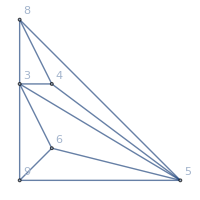
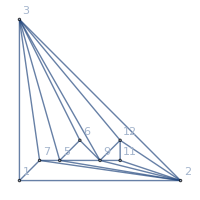
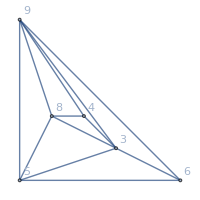
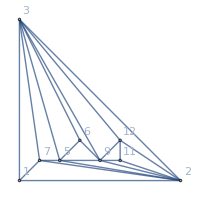
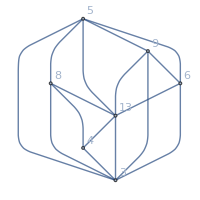
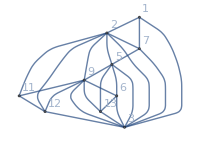
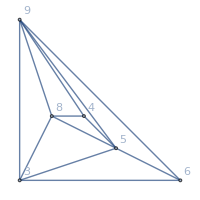
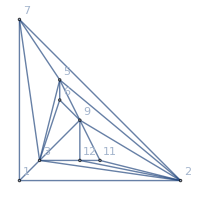
-Graphics-{(-3+x)^2 (-2+x)^2,48} | -Graphics-{(-3+x)^6 (-2+x),24}
-Graphics-{(-3+x)^3 (-2+x),24} | -Graphics-{(-3+x)^6 (-2+x),24}
-Graphics-{(-4+x) (-3+x)^3 (-2+x),0} | -Graphics-{(-4+x) (-3+x)^6 (-2+x),0}
-Graphics-{(-3+x)^3 (-2+x),24} | -Graphics-{(-3+x)^6 (-2+x),24}
-Graphics-{(-4+x) (-3+x)^3 (-2+x),0} | -Graphics-{(-4+x) (-3+x)^6 (-2+x),0}
-Graphics-{(-4+x)^2 (-3+x)^2 (-2+x),0} | -Graphics-{(-4+x) (-3+x)^6 (-2+x),0}
-Graphics-{(-4+x)^2 (-3+x)^2 (-2+x),0} | -Graphics-{(-4+x) (-3+x)^6 (-2+x),0}
-Graphics-{(-5+x) (-4+x)^2 (-3+x)^2 (-2+x),0} | -Graphics-{(-5+x) (-4+x) (-3+x)^6 (-2+x),0}6

```mathematica
With [{g=ReadGrof[20048],border={3,5,9,13,10}},
Labeled[TableForm[Map[{#[[2]],#[[3]]}&,ZykovDecomposition23[g,border]]],Style[EdgeCount[Subgraph[g,border]],Red,36],Top]
]
```

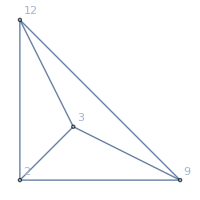
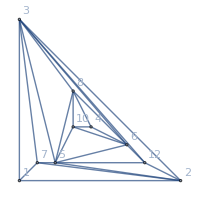
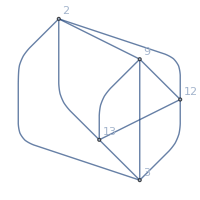
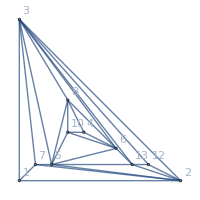
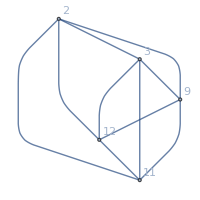
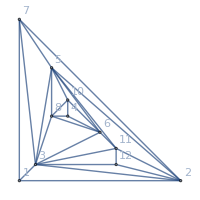
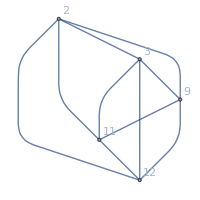
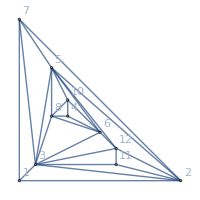
-Graphics-{(-3+x) (-2+x),24} | -Graphics-{(-3+x)^7 (-2+x),24}
-Graphics-{(-4+x) (-3+x) (-2+x),0} | -Graphics-{(-3+x)^8 (-2+x),24}
-Graphics-{(-4+x) (-3+x) (-2+x),0} | -Graphics-{(-3+x)^8 (-2+x),24}
-Graphics-{(-4+x) (-3+x) (-2+x),0} | -Graphics-{(-3+x)^8 (-2+x),24}
-Graphics-{(-5+x) (-4+x) (-3+x) (-2+x),0} | -Graphics-{(-4+x) (-3+x)^8 (-2+x),0}7

```mathematica
With [{g=ReadGrof[20050],border={2,3,11,12,13}},
Labeled[TableForm[Map[{#[[2]],#[[3]]}&,ZykovDecomposition23[g,border]]],Style[EdgeCount[Subgraph[g,border]],Red,36],Top]
]
```

```mathematica
With [{g=ReadGrof[20049],border={3,5,13,4,10}},
{EdgeCount[Subgraph[g,border]],Length[Select[Map[#[[1]]*#[[2]]&,Map[{ChromaticPolynomial[#[[2]][[1]],4],ChromaticPolynomial[#[[3]][[1]],4]}&,ZykovDecomposition23[g,border]]],#≠0&]]}
]
```

{5,3}

```mathematica
result=Flatten[Monitor[Table[
Block[{g=ReadGrof[k], adj},
Table[
adj=AdjacencyList[g,v];
With[{h=Subgraph[g,adj]},

{k,Grid[{adj},Frame->All],EdgeCount[Subgraph[g,adj]],Length[Select[Map[#[[1]]*#[[2]]&,Map[{ChromaticPolynomial[#[[2]][[1]],4],ChromaticPolynomial[#[[3]][[1]],4]}&,ZykovDecomposition23[g,adj]]],#≠0&]]}
]
,{v,Select[VertexList[g],VertexDegree[g,#]==5&]}
]
],
{k,20000,21000}],{k,v}],1];Length[result]
```

2634

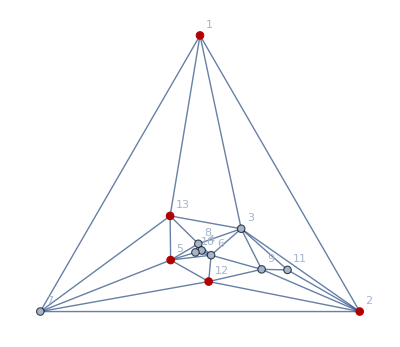

```mathematica
Graph[ReadGrof[20225],VertexLabels->"Name",GraphLayout->"TutteEmbedding",GraphHighlight->{1,2,13,12,5}]
```

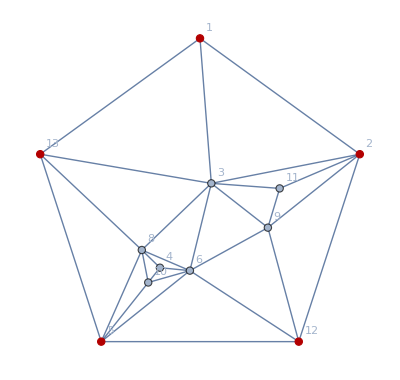

```mathematica
Graph[VertexDelete[ReadGrof[20225],7],VertexLabels->"Name",GraphLayout->"TutteEmbedding",GraphHighlight->{1,2,13,12,5}]
```

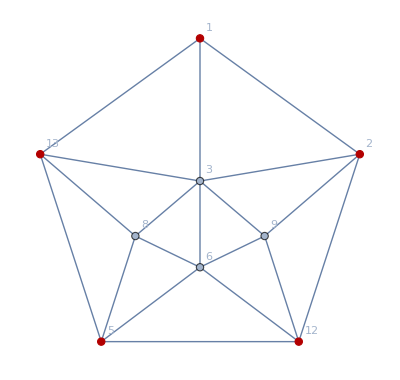

```mathematica
Graph[VertexDelete[ReadGrof[20225],{7,11,4,10}],VertexLabels->"Name",GraphLayout->"TutteEmbedding",GraphHighlight->{1,2,13,12,5}]
```

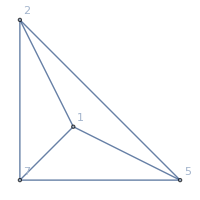
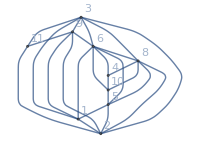
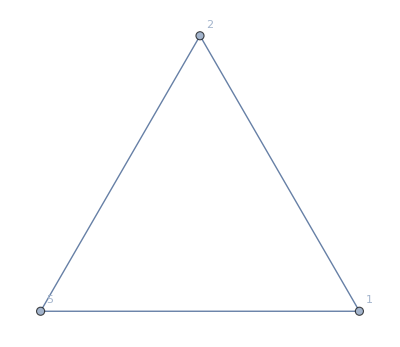
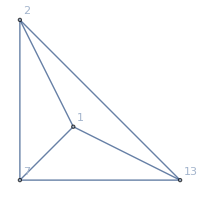
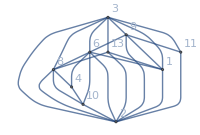
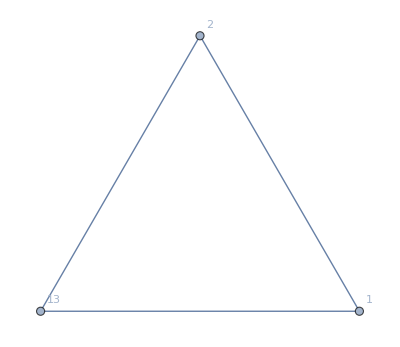
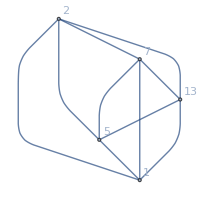
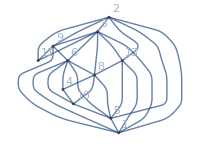
{{{{1,12},{2,13},{5}},-Graphics-{(-3+x) (-2+x),24},-Graphics-{(-3+x)^5 (-2+x) (15-7 x+x^2),72},-Graphics-{-2+x,24},(-3+x) (-2+x) (-1+x) x,(-3+x)^5 (-2+x) (-1+x) x (15-7 x+x^2),(-2+x) (-1+x) x,{v1x2x5x7},{v18bx26x3ax459,v18bx26x345x9a,v1abx26x345x89},{v1x2x5}},{{{1,12},{2,5},{13}},-Graphics-{(-3+x) (-2+x),24},-Graphics-{(-4+x) (-3+x)^4 (-2+x) (13-7 x+x^2),0},-Graphics-{-2+x,24},(-3+x) (-2+x) (-1+x) x,(-4+x) (-3+x)^4 (-2+x) (-1+x) x (13-7 x+x^2),(-2+x) (-1+x) x,{v1x2x7xd},{},{v1x2xd}},{{{1,12},{2},{5},{13}},-Graphics-{(-4+x) (-3+x) (-2+x),0},-Graphics-{(-3+x)^4 (-2+x) (193-196 x+77 x^2-14 x^3+x^4),24},-Graphics-{(-3+x) (-2+x),24},(-4+x) (-3+x) (-2+x) (-1+x) x,(-3+x)^4 (-2+x) (-1+x) x (193-196 x+77 x^2-14 x^3+x^4),(-3+x) (-2+x) (-1+x) x,{},{v18bx26x345x9ad},{v1x2x5xd}},{{{1,5},{2,13},{12}},-Graphics-{(-3+x) (-2+x),24},-Graphics-{(-3+x)^5 (-2+x) (15-7 x+x^2),72},-Graphics-{-2+x,24},(-3+x) (-2+x) (-1+x) x,(-3+x)^5 (-2+x) (-1+x) x (15-7 x+x^2),(-2+x) (-1+x) x,{v1x2x7xc},{v149x26x3ax8bc,v149x26x3acx8b,v14bx26x3acx89},{v1x2xc}},{{{1,5},{2},{12,13}},-Graphics-{(-3+x) (-2+x),24},-Graphics-{(-4+x) (-3+x)^4 (-2+x) (13-7 x+x^2),0},-Graphics-{-2+x,24},(-3+x) (-2+x) (-1+x) x,(-4+x) (-3+x)^4 (-2+x) (-1+x) x (13-7 x+x^2),(-2+x) (-1+x) x,{v1x2x7xc},{},{v1x2xc}},{{{1,5},{2},{12},{13}},-Graphics-{(-4+x) (-3+x) (-2+x),0},-Graphics-{(-3+x)^4 (-2+x) (193-196 x+77 x^2-14 x^3+x^4),24},-Graphics-{(-3+x) (-2+x),24},(-4+x) (-3+x) (-2+x) (-1+x) x,(-3+x)^4 (-2+x) (-1+x) x (193-196 x+77 x^2-14 x^3+x^4),(-3+x) (-2+x) (-1+x) x,{},{v149x28x3acx6bd},{v1x2xcxd}},{{{1},{2,13},{5},{12}},-Graphics-{(-4+x) (-3+x) (-2+x),0},-Graphics-{(-3+x)^4 (-2+x) (160-167 x+68 x^2-13 x^3+x^4),96},-Graphics-{(-3+x) (-2+x),24},(-4+x) (-3+x) (-2+x) (-1+x) x,(-3+x)^4 (-2+x) (-1+x) x (160-167 x+68 x^2-13 x^3+x^4),(-3+x) (-2+x) (-1+x) x,{},{v18bx26x3acx459,v19ax26x345x8bc,v189x26x345xabc,v189x26x3acx45b},{v1x2x5xc}},{{{1},{2,5},{12,13}},-Graphics-{(-3+x) (-2+x),24},-Graphics-{(-4+x)^2 (-3+x)^5 (-2+x),0},-Graphics-{-2+x,24},(-3+x) (-2+x) (-1+x) x,(-4+x)^2 (-3+x)^5 (-2+x) (-1+x) x,(-2+x) (-1+x) x,{v1x2x7xc},{},{v1x2xc}},{{{1},{2,5},{12},{13}},-Graphics-{(-4+x) (-3+x) (-2+x),0},-Graphics-{(-3+x)^4 (-2+x) (181-189 x+76 x^2-14 x^3+x^4),24},-Graphics-{(-3+x) (-2+x),24},(-4+x) (-3+x) (-2+x) (-1+x) x,(-3+x)^4 (-2+x) (-1+x) x (181-189 x+76 x^2-14 x^3+x^4),(-3+x) (-2+x) (-1+x) x,{},{v189x24x3acx6bd},{v1x2xcxd}},{{{1},{2},{5},{12,13}},-Graphics-{(-4+x) (-3+x) (-2+x),0},-Graphics-{(-3+x)^4 (-2+x) (181-189 x+76 x^2-14 x^3+x^4),24},-Graphics-{(-3+x) (-2+x),24},(-4+x) (-3+x) (-2+x) (-1+x) x,(-3+x)^4 (-2+x) (-1+x) x (181-189 x+76 x^2-14 x^3+x^4),(-3+x) (-2+x) (-1+x) x,{},{v189x26x345xabc},{v1x2x5xc}},{{{1},{2},{5},{12},{13}},-Graphics-{(-5+x) (-4+x) (-3+x) (-2+x),0},-Graphics-{(-4+x) (-3+x)^4 (-2+x) (218-210 x+79 x^2-14 x^3+x^4),0},-Graphics-{(-4+x) (-3+x) (-2+x),0},(-5+x) (-4+x) (-3+x) (-2+x) (-1+x) x,(-4+x) (-3+x)^4 (-2+x) (-1+x) x (218-210 x+79 x^2-14 x^3+x^4),(-4+x) (-3+x) (-2+x) (-1+x) x,{},{},{}}}

```mathematica
With[{g=ReadGrof[20225]},ZykovDecomposition23[g,{1,2,13,12,5}]]
```

```mathematica
Select[result,#[[3]]==5&&#[[4]]==2&]
```

{{20225,1 | 2 | 13 | 12 | 5,5,2},{20225,2 | 7 | 9 | 6 | 5,5,2},{20246,2 | 12 | 13 | 8 | 10,5,2},{20246,2 | 5 | 9 | 6 | 10,5,2},{20286,2 | 9 | 13 | 6 | 10,5,2},{20286,2 | 7 | 5 | 12 | 10,5,2},{20288,3 | 7 | 5 | 8 | 10,5,2},{20319,3 | 5 | 12 | 4 | 10,5,2},{20319,3 | 9 | 8 | 4 | 13,5,2},{20319,8 | 12 | 6 | 10 | 13,5,2},{20319,5 | 9 | 4 | 10 | 13,5,2},{20324,2 | 9 | 13 | 6 | 10,5,2},{20461,1 | 2 | 13 | 12 | 5,5,2},{20461,2 | 7 | 9 | 6 | 5,5,2},{20478,2 | 7 | 5 | 13 | 8,5,2},{20478,3 | 7 | 12 | 6 | 8,5,2},{20483,2 | 12 | 13 | 8 | 10,5,2},{20483,2 | 5 | 9 | 6 | 10,5,2},{20494,2 | 3 | 7 | 12 | 13,5,2},{20494,1 | 3 | 12 | 6 | 8,5,2},{20542,2 | 9 | 13 | 6 | 10,5,2},{20542,2 | 7 | 5 | 12 | 10,5,2},{20544,3 | 7 | 5 | 8 | 10,5,2},{20562,2 | 9 | 13 | 6 | 10,5,2},{20570,3 | 5 | 6 | 4 | 10,5,2},{20570,6 | 8 | 10 | 12 | 13,5,2},{20570,5 | 9 | 4 | 10 | 13,5,2},{20677,2 | 5 | 12 | 8 | 10,5,2},{20678,2 | 3 | 11 | 6 | 5,5,2},{20678,2 | 11 | 12 | 8 | 5,5,2},{20690,2 | 3 | 7 | 12 | 13,5,2},{20690,1 | 2 | 13 | 9 | 6,5,2},{20690,1 | 3 | 12 | 6 | 8,5,2},{20707,2 | 7 | 5 | 12 | 10,5,2},{20708,2 | 3 | 9 | 8 | 6,5,2},{20709,3 | 7 | 5 | 8 | 10,5,2},{20755,3 | 5 | 12 | 4 | 10,5,2},{20755,3 | 9 | 8 | 4 | 13,5,2},{20755,8 | 12 | 6 | 10 | 13,5,2},{20755,5 | 9 | 4 | 10 | 13,5,2},{20896,2 | 7 | 5 | 13 | 8,5,2},{20896,3 | 7 | 12 | 6 | 8,5,2},{20903,2 | 5 | 12 | 8 | 10,5,2},{20911,2 | 3 | 7 | 12 | 13,5,2},{20911,1 | 2 | 13 | 9 | 6,5,2},{20911,1 | 3 | 12 | 6 | 8,5,2},{20959,2 | 7 | 5 | 12 | 10,5,2},{20961,3 | 7 | 5 | 8 | 10,5,2},{20997,3 | 5 | 12 | 4 | 10,5,2},{20997,3 | 9 | 8 | 4 | 13,5,2},{20997,8 | 12 | 6 | 10 | 13,5,2}}

```mathematica
Graph[ReadGrof[20000],VertexLabels->"Name",GraphLayout->"PlanarEmbedding",GraphHighlight->{9,6,4,10,13}]
```

-Graphics-

```mathematica
Graph[VertexDelete[ReadGrof[20000],{12,1,7,2,11}],VertexLabels->"Name",GraphLayout->"TutteEmbedding",GraphHighlight->{9,6,4,10,13}]
```

-Graphics-

```mathematica
Select[result,#[[3]]==5&&#[[4]]==3&]
```

{{20000,9 | 6 | 4 | 10 | 13,5,3},{20029,3 | 5 | 13 | 4 | 10,5,3},{20029,3 | 9 | 8 | 4 | 6,5,3},{20029,5 | 9 | 13 | 4 | 10,5,3},{20031,2 | 5 | 9 | 6 | 10,5,3},{20049,3 | 5 | 13 | 4 | 10,5,3},{20049,3 | 9 | 8 | 4 | 6,5,3},{20049,5 | 9 | 13 | 4 | 10,5,3},{20051,2 | 5 | 9 | 6 | 10,5,3},{20068,3 | 5 | 13 | 4 | 10,5,3},{20068,3 | 9 | 8 | 4 | 6,5,3},{20068,5 | 9 | 13 | 4 | 10,5,3},{20069,2 | 5 | 9 | 6 | 10,5,3},{20087,2 | 5 | 9 | 6 | 10,5,3},{20088,3 | 5 | 6 | 4 | 10,5,3},{20088,5 | 9 | 6 | 4 | 10,5,3},{20103,3 | 5 | 13 | 4 | 10,5,3},{20103,3 | 9 | 8 | 4 | 6,5,3},{20103,5 | 9 | 13 | 4 | 10,5,3},{20118,3 | 5 | 13 | 4 | 10,5,3},{20118,3 | 9 | 8 | 4 | 6,5,3},{20135,3 | 5 | 6 | 4 | 10,5,3},{20135,5 | 9 | 6 | 4 | 10,5,3},{20162,2 | 7 | 6 | 5 | 10,5,3},{20163,2 | 5 | 6 | 4 | 12,5,3},{20163,3 | 5 | 6 | 4 | 12,5,3},{20167,2 | 7 | 6 | 5 | 12,5,3},{20187,3 | 5 | 13 | 4 | 10,5,3},{20187,3 | 9 | 8 | 4 | 6,5,3},{20198,3 | 9 | 8 | 4 | 6,5,3},{20198,5 | 9 | 13 | 4 | 10,5,3},{20199,2 | 5 | 9 | 6 | 10,5,3},{20203,2 | 3 | 7 | 12 | 13,5,3},{20203,1 | 7 | 13 | 9 | 5,5,3},{20207,1 | 3 | 12 | 13 | 5,5,3},{20214,3 | 5 | 13 | 4 | 10,5,3},{20214,3 | 9 | 8 | 4 | 6,5,3},{20214,9 | 5 | 13 | 4 | 10,5,3},{20215,1 | 2 | 7 | 9 | 13,5,3},{20215,7 | 12 | 9 | 5 | 6,5,3},{20219,2 | 7 | 9 | 6 | 13,5,3},{20226,7 | 12 | 6 | 13 | 10,5,3},{20229,3 | 9 | 8 | 4 | 6,5,3},{20241,2 | 7 | 13 | 5 | 8,5,3},{20242,3 | 9 | 8 | 4 | 6,5,3},{20243,3 | 12 | 6 | 4 | 8,5,3},{20244,3 | 9 | 12 | 6 | 8,5,3},{20245,2 | 9 | 12 | 8 | 5,5,3},{20256,2 | 7 | 12 | 9 | 5,5,3},{20275,3 | 5 | 13 | 4 | 10,5,3},{20275,3 | 9 | 8 | 4 | 6,5,3},{20275,9 | 5 | 13 | 4 | 10,5,3},{20280,3 | 7 | 8 | 10 | 13,5,3},{20288,3 | 12 | 13 | 4 | 10,5,3},{20288,3 | 9 | 8 | 4 | 6,5,3},{20288,5 | 9 | 13 | 4 | 10,5,3},{20288,5 | 8 | 12 | 4 | 6,5,3},{20289,3 | 9 | 12 | 6 | 8,5,3},{20298,1 | 3 | 7 | 5 | 12,5,3},{20310,3 | 12 | 13 | 4 | 10,5,3},{20317,2 | 5 | 9 | 6 | 10,5,3},{20318,3 | 9 | 12 | 10 | 13,5,3},{20318,5 | 9 | 6 | 8 | 10,5,3},{20320,3 | 5 | 12 | 4 | 10,5,3},{20322,9 | 12 | 4 | 10 | 13,5,3},{20360,2 | 5 | 9 | 6 | 10,5,3},{20361,3 | 5 | 6 | 4 | 10,5,3},{20361,5 | 9 | 6 | 4 | 10,5,3},{20381,2 | 5 | 9 | 6 | 10,5,3},{20382,3 | 5 | 6 | 4 | 10,5,3},{20382,5 | 9 | 6 | 4 | 10,5,3},{20398,2 | 5 | 9 | 6 | 10,5,3},{20399,3 | 5 | 6 | 4 | 10,5,3},{20399,5 | 9 | 6 | 4 | 10,5,3},{20436,2 | 5 | 9 | 6 | 10,5,3},{20437,5 | 9 | 6 | 4 | 10,5,3},{20440,2 | 3 | 7 | 12 | 13,5,3},{20440,1 | 7 | 13 | 9 | 5,5,3},{20443,1 | 3 | 12 | 13 | 5,5,3},{20449,3 | 5 | 6 | 4 | 10,5,3},{20449,9 | 5 | 6 | 4 | 10,5,3},{20450,1 | 2 | 7 | 9 | 13,5,3},{20450,7 | 12 | 9 | 5 | 6,5,3},{20455,2 | 7 | 9 | 6 | 13,5,3},{20462,2 | 7 | 9 | 6 | 5,5,3},{20463,7 | 12 | 6 | 13 | 10,5,3},{20477,2 | 7 | 13 | 5 | 8,5,3},{20480,3 | 12 | 6 | 4 | 8,5,3},{20482,2 | 9 | 12 | 8 | 5,5,3},{20488,2 | 3 | 7 | 12 | 13,5,3},{20488,1 | 7 | 13 | 5 | 8,5,3},{20497,2 | 7 | 12 | 9 | 5,5,3},{20515,3 | 5 | 6 | 4 | 10,5,3},{20515,9 | 5 | 6 | 4 | 10,5,3},{20517,1 | 2 | 13 | 5 | 12,5,3},{20526,2 | 7 | 9 | 12 | 5,5,3},{20527,3 | 7 | 5 | 6 | 8,5,3},{20531,3 | 7 | 6 | 8 | 13,5,3},{20535,1 | 3 | 7 | 5 | 9,5,3},{20536,3 | 7 | 8 | 10 | 13,5,3},{20544,3 | 6 | 12 | 4 | 10,5,3},{20544,5 | 8 | 12 | 4 | 13,5,3},{20544,5 | 9 | 6 | 4 | 10,5,3},{20556,2 | 5 | 9 | 6 | 10,5,3},{20557,5 | 9 | 6 | 8 | 10,5,3},{20571,3 | 5 | 6 | 4 | 10,5,3},{20572,3 | 5 | 6 | 4 | 10,5,3},{20573,3 | 5 | 6 | 4 | 10,5,3},{20575,3 | 6 | 13 | 4 | 10,5,3},{20576,9 | 6 | 4 | 10 | 13,5,3},{20603,3 | 5 | 13 | 4 | 10,5,3},{20603,3 | 9 | 8 | 4 | 6,5,3},{20603,5 | 9 | 13 | 4 | 10,5,3},{20618,3 | 5 | 13 | 4 | 10,5,3},{20618,3 | 9 | 8 | 4 | 6,5,3},{20618,5 | 9 | 13 | 4 | 10,5,3},{20633,3 | 5 | 13 | 4 | 10,5,3},{20633,3 | 9 | 8 | 4 | 6,5,3},{20633,5 | 9 | 13 | 4 | 10,5,3},{20644,3 | 5 | 13 | 4 | 10,5,3},{20644,3 | 9 | 8 | 4 | 6,5,3},{20653,3 | 5 | 13 | 4 | 10,5,3},{20653,3 | 9 | 8 | 4 | 6,5,3},{20660,3 | 9 | 8 | 4 | 6,5,3},{20660,5 | 9 | 13 | 4 | 10,5,3},{20671,2 | 7 | 13 | 5 | 8,5,3},{20672,2 | 3 | 9 | 8 | 6,5,3},{20673,3 | 9 | 8 | 4 | 6,5,3},{20674,3 | 12 | 6 | 4 | 8,5,3},{20675,3 | 9 | 12 | 6 | 8,5,3},{20684,2 | 3 | 7 | 12 | 13,5,3},{20684,1 | 7 | 13 | 5 | 8,5,3},{20693,1 | 2 | 12 | 9 | 13,5,3},{20709,3 | 12 | 13 | 4 | 10,5,3},{20709,3 | 9 | 8 | 4 | 6,5,3},{20709,5 | 9 | 13 | 4 | 10,5,3},{20709,5 | 8 | 12 | 4 | 6,5,3},{20710,3 | 9 | 12 | 6 | 8,5,3},{20719,1 | 2 | 13 | 9 | 12,5,3},{20719,1 | 3 | 7 | 5 | 12,5,3},{20722,5 | 9 | 4 | 10 | 13,5,3},{20722,5 | 12 | 4 | 10 | 13,5,3},{20722,9 | 12 | 4 | 6 | 8,5,3},{20734,2 | 3 | 9 | 8 | 6,5,3},{20736,3 | 12 | 13 | 4 | 10,5,3},{20748,9 | 12 | 8 | 4 | 6,5,3},{20749,2 | 3 | 9 | 8 | 6,5,3},{20754,3 | 9 | 12 | 10 | 13,5,3},{20754,5 | 9 | 6 | 8 | 10,5,3},{20756,3 | 5 | 12 | 4 | 10,5,3},{20757,9 | 12 | 4 | 10 | 13,5,3},{20768,2 | 3 | 9 | 6 | 12,5,3},{20778,3 | 9 | 13 | 6 | 8,5,3},{20779,3 | 9 | 10 | 8 | 13,5,3},{20794,2 | 3 | 9 | 10 | 12,5,3},{20795,2 | 3 | 9 | 12 | 6,5,3},{20831,3 | 5 | 13 | 4 | 10,5,3},{20831,3 | 9 | 8 | 4 | 6,5,3},{20846,3 | 5 | 13 | 4 | 10,5,3},{20846,3 | 9 | 8 | 4 | 6,5,3},{20857,3 | 5 | 13 | 4 | 10,5,3},{20857,3 | 9 | 8 | 4 | 6,5,3},{20867,3 | 9 | 8 | 4 | 6,5,3},{20871,2 | 3 | 7 | 12 | 13,5,3},{20871,1 | 7 | 13 | 9 | 5,5,3},{20875,1 | 3 | 12 | 13 | 5,5,3},{20881,3 | 5 | 13 | 4 | 10,5,3},{20881,3 | 9 | 8 | 4 | 6,5,3},{20895,2 | 7 | 13 | 5 | 8,5,3},{20898,3 | 9 | 8 | 4 | 6,5,3},{20899,3 | 12 | 6 | 4 | 8,5,3},{20901,3 | 9 | 12 | 6 | 8,5,3},{20902,2 | 9 | 12 | 8 | 5,5,3},{20906,2 | 3 | 7 | 12 | 13,5,3},{20906,1 | 7 | 13 | 5 | 8,5,3},{20914,2 | 7 | 12 | 9 | 5,5,3},{20929,3 | 5 | 13 | 4 | 10,5,3},{20929,3 | 9 | 8 | 4 | 6,5,3},{20935,1 | 2 | 13 | 5 | 12,5,3},{20944,2 | 7 | 9 | 12 | 5,5,3},{20947,3 | 7 | 6 | 8 | 13,5,3},{20949,1 | 3 | 7 | 5 | 9,5,3},{20953,3 | 7 | 8 | 10 | 13,5,3},{20961,3 | 12 | 13 | 4 | 10,5,3},{20961,3 | 9 | 8 | 4 | 6,5,3},{20961,5 | 8 | 12 | 4 | 6,5,3},{20962,3 | 9 | 12 | 6 | 8,5,3},{20963,7 | 5 | 6 | 12 | 10,5,3},{20971,1 | 3 | 7 | 5 | 9,5,3},{20971,1 | 2 | 13 | 9 | 12,5,3},{20971,1 | 3 | 7 | 5 | 12,5,3},{20974,5 | 12 | 4 | 10 | 13,5,3},{20974,9 | 12 | 4 | 6 | 8,5,3},{20990,3 | 12 | 13 | 4 | 10,5,3},{20998,3 | 5 | 12 | 4 | 10,5,3},{20999,3 | 7 | 5 | 12 | 8,5,3}}

```mathematica
Graph[VertexDelete[ReadGrof[20000],{13,1,11,7,2}],VertexLabels->"Name",GraphLayout->"TutteEmbedding",GraphHighlight->{5,9,8,10,12}]
```

-Graphics-

```mathematica
Take[Select[result,#[[3]]==5&&#[[4]]==5&],10]
```

{{20019,1 | 2 | 7 | 9 | 5,5,5},{20020,2 | 7 | 9 | 5 | 6,5,5},{20022,1 | 3 | 7 | 5 | 8,5,5},{20024,3 | 7 | 5 | 8 | 10,5,5},{20043,1 | 3 | 7 | 5 | 8,5,5},{20044,3 | 7 | 5 | 8 | 10,5,5},{20059,1 | 2 | 7 | 9 | 5,5,5},{20060,2 | 7 | 9 | 5 | 6,5,5},{20063,3 | 7 | 5 | 8 | 10,5,5},{20078,1 | 2 | 7 | 9 | 5,5,5}}

```mathematica
Graph[VertexDelete[ReadGrof[20020],{13,
11,1,12,4,10,8}],VertexLabels->"Name",GraphLayout->"TutteEmbedding",GraphHighlight->{2,7,9,5,6}]
```

-Graphics-

```mathematica
Graph[VertexDelete[ReadGrof[20022],{13,4,10,11,12}],VertexLabels->"Name",GraphLayout->"TutteEmbedding",GraphHighlight->{1,3,7,5,8}]
```

-Graphics-

```mathematica
Graph[VertexDelete[ReadGrof[20024],{13,1,4,11,12}],VertexLabels->"Name",GraphLayout->"TutteEmbedding",GraphHighlight->{3,7,5,8,10}]
```

-Graphics-

```mathematica
Graph[VertexDelete[ReadGrof[20024],{13,1,4,11,12}],VertexLabels->"Name",GraphLayout->"TutteEmbedding",GraphHighlight->{3,7,5,8,10}]
```

```mathematica
DeleteVertices[g_Graph,border_]:=Block[{result=g,three,center=VertexList[g]},
Table[center=Select[center,EdgeQ[g,#<->v]&],{v,border}];
DeleteVertices[result,border,center]
]
```

```mathematica
DeleteVertices[g_Graph,border_, center_]:=Block[{result=g,three},
result=VertexDelete[result,center];
three=Select[VertexList[result],!MemberQ[border,#]&&VertexDegree[result,#]==3&];
While[three≠{},
result=VertexDelete[result,three];
three=Select[VertexList[result],!MemberQ[border,#]&&VertexDegree[result,#]==3&];
];
Graph[result,GraphLayout->"TutteEmbedding",GraphHighlight->border,VertexLabels->"Name"]
]
```

```mathematica
DeleteVertices[ReadGrof[20024],{3,7,5,8,10}]
```

-Graphics-

```mathematica
DeleteVertices[ReadGrof[20024],{3,7,5,8,10}]
```

```mathematica
DeleteVertices[ReadGrof[20043],{1,3,7,5,8}]
```

-Graphics-

```mathematica
Graph[ReadGrof[20078],GraphLayout->"PlanarEmbedding",VertexLabels->"Name",GraphHighlight->{1,2,7,9,5}]
```

-Graphics-

```mathematica
Graph[VertexDelete[ReadGrof[20078],{13,4,12,11,10,8,6}],GraphLayout->"TutteEmbedding",VertexLabels->"Name",GraphHighlight->{1,2,7,9,5}]
```

-Graphics-

```mathematica
DeleteVertices[ReadGrof[20063],{3,7,5,8,10}]
```

-Graphics-

```mathematica
DeleteVertices[ReadGrof[20078],{1,2,7,9,5},13]
```

```mathematica
Select[result,#[[3]]==5&&#[[4]]==4&]
```

{{20000,5 | 9 | 8 | 10 | 12,5,4},{20209,3 | 7 | 12 | 8 | 5,5,4},{20215,1 | 3 | 12 | 5 | 13,5,4},{20216,12 | 9 | 5 | 6 | 10,5,4},{20254,3 | 9 | 8 | 4 | 6,5,4},{20255,3 | 12 | 6 | 4 | 8,5,4},{20257,2 | 5 | 9 | 6 | 10,5,4},{20260,1 | 2 | 12 | 5 | 13,5,4},{20260,1 | 3 | 7 | 8 | 13,5,4},{20260,7 | 12 | 5 | 8 | 10,5,4},{20287,3 | 5 | 9 | 13 | 10,5,4},{20287,3 | 7 | 5 | 8 | 10,5,4},{20310,3 | 5 | 8 | 6 | 10,5,4},{20310,3 | 9 | 8 | 4 | 6,5,4},{20317,3 | 9 | 13 | 12 | 10,5,4},{20321,2 | 5 | 9 | 6 | 10,5,4},{20321,3 | 5 | 12 | 4 | 10,5,4},{20321,3 | 9 | 8 | 4 | 6,5,4},{20321,9 | 13 | 12 | 4 | 10,5,4},{20321,5 | 13 | 8 | 4 | 6,5,4},{20322,3 | 9 | 8 | 4 | 6,5,4},{20322,5 | 9 | 8 | 6 | 10,5,4},{20330,3 | 9 | 12 | 8 | 6,5,4},{20445,3 | 7 | 12 | 8 | 5,5,4},{20450,1 | 3 | 12 | 5 | 13,5,4},{20451,12 | 9 | 5 | 6 | 10,5,4},{20488,1 | 3 | 7 | 5 | 9,5,4},{20496,3 | 12 | 6 | 4 | 8,5,4},{20498,2 | 5 | 9 | 6 | 10,5,4},{20502,1 | 3 | 7 | 5 | 9,5,4},{20502,1 | 2 | 12 | 5 | 13,5,4},{20502,1 | 3 | 7 | 8 | 13,5,4},{20502,7 | 12 | 5 | 8 | 10,5,4},{20517,1 | 3 | 7 | 5 | 9,5,4},{20520,2 | 3 | 5 | 11 | 6,5,4},{20528,3 | 7 | 5 | 6 | 8,5,4},{20543,3 | 7 | 5 | 8 | 10,5,4},{20569,2 | 5 | 9 | 10 | 13,5,4},{20569,3 | 5 | 6 | 4 | 10,5,4},{20569,5 | 12 | 8 | 4 | 13,5,4},{20569,9 | 12 | 6 | 4 | 10,5,4},{20575,3 | 5 | 8 | 10 | 12,5,4},{20576,5 | 9 | 8 | 10 | 12,5,4},{20664,2 | 3 | 11 | 6 | 5,5,4},{20691,3 | 9 | 8 | 4 | 6,5,4},{20692,3 | 12 | 6 | 4 | 8,5,4},{20696,1 | 2 | 12 | 5 | 13,5,4},{20696,1 | 3 | 7 | 8 | 13,5,4},{20696,7 | 12 | 5 | 8 | 10,5,4},{20736,3 | 5 | 8 | 6 | 10,5,4},{20736,3 | 9 | 8 | 4 | 6,5,4},{20757,3 | 9 | 8 | 4 | 6,5,4},{20757,5 | 9 | 8 | 6 | 10,5,4},{20769,5 | 9 | 11 | 8 | 12,5,4},{20793,3 | 7 | 5 | 12 | 10,5,4},{20877,3 | 7 | 12 | 8 | 5,5,4},{20906,1 | 3 | 7 | 5 | 9,5,4},{20912,3 | 9 | 8 | 4 | 6,5,4},{20913,3 | 12 | 6 | 4 | 8,5,4},{20916,1 | 3 | 7 | 5 | 9,5,4},{20916,1 | 2 | 12 | 5 | 13,5,4},{20916,1 | 3 | 7 | 8 | 13,5,4},{20916,7 | 12 | 5 | 8 | 10,5,4},{20935,1 | 3 | 7 | 5 | 9,5,4},{20960,3 | 7 | 5 | 8 | 10,5,4},{20990,3 | 5 | 8 | 6 | 10,5,4},{20990,3 | 9 | 8 | 4 | 6,5,4}}

```mathematica
Map[Labeled[DeleteVertices[ReadGrof[#[[1]]],#[[2,1,1]]],{#[[1]],#[[2,1,1]]}]&,Take[Select[result,#[[3]]==5&&#[[4]]==4&],10]]
```

{-Graphics-{20000,{5,9,8,10,12}},-Graphics-{20209,{3,7,12,8,5}},-Graphics-{20215,{1,3,12,5,13}},-Graphics-{20216,{12,9,5,6,10}},-Graphics-{20254,{3,9,8,4,6}},-Graphics-{20255,{3,12,6,4,8}},-Graphics-{20257,{2,5,9,6,10}},-Graphics-{20260,{1,2,12,5,13}},-Graphics-{20260,{1,3,7,8,13}},-Graphics-{20260,{7,12,5,8,10}}}

```mathematica
DeleteVertices[ReadGrof[20000],{5,9,8,10,12}]
```

-Graphics-

```mathematica
DeleteVertices[ReadGrof[20990],{3,9,8,4,6}]
```

-Graphics-

```mathematica
First[Map[{#[[3]],#[[4]]}&,result]//Tally//Sort]
```

{{5,2},51}

```mathematica
Map[{#[[3]],#[[4]]}&,result]//Tally//Sort
```

{{{5,2},51},{{5,3},196},{{5,4},67},{{5,5},214},{{6,2},542},{{6,3},546},{{7,1},1018}}

```mathematica
Map[First,Map[{#[[3]],#[[4]]}&,result]//Tally//Sort]
```

{{5,2},{5,3},{5,4},{5,5},{6,2},{6,3},{7,1}}

```mathematica
ListLinePlot[{51,196,67,214}]
```

-Graphics-

```mathematica
result2=Flatten[Monitor[Table[
Block[{g=ReadGrof[k], adj},
Table[
adj=AdjacencyList[g,v];
With[{h=Subgraph[g,adj]},

{k,Grid[{adj},Frame->All],EdgeCount[Subgraph[g,adj]],Length[Select[Map[#[[1]]*#[[2]]&,Map[{ChromaticPolynomial[#[[2]][[1]],4],ChromaticPolynomial[#[[3]][[1]],4]}&,ZykovDecomposition23[g,adj]]],#≠0&]]}
]
,{v,Select[VertexList[g],VertexDegree[g,#]==4&]}
]
],
{k,20000,20050}],{k,v}],1];Length[result2]
```

140

```mathematica
Map[{#[[3]],#[[4]]}&,result2]//Tally//Sort
```

```mathematica
{{{4,2},1},{{4,3},5},{{5,1},21}}
```

```mathematica
result3=Flatten[Monitor[Table[
Block[{g=ReadGrof[k], adj},
Table[
adj=AdjacencyList[g,v];
With[{h=Subgraph[g,adj]},

{k,Grid[{adj},Frame->All],EdgeCount[Subgraph[g,adj]],Length[Select[Map[#[[1]]*#[[2]]&,Map[{ChromaticPolynomial[#[[2]][[1]],4],ChromaticPolynomial[#[[3]][[1]],4]}&,ZykovDecomposition23[g,adj]]],#≠0&]]}
]
,{v,Select[VertexList[g],VertexDegree[g,#]==3&]}
]
],
{k,20000,20050}],{k,v}],1];Length[result3]
```

163

```mathematica
Map[{#[[3]],#[[4]]}&,result3]//Tally//Sort
```

{{{3,1},163}}

```mathematica
result6=Flatten[Monitor[Table[
Block[{g=ReadGrof[k], adj},
Table[
adj=AdjacencyList[g,v];
With[{h=Subgraph[g,adj]},

{k,Grid[{adj},Frame->All],EdgeCount[Subgraph[g,adj]],Length[Select[Map[#[[1]]*#[[2]]&,Map[{ChromaticPolynomial[#[[2]][[1]],4],ChromaticPolynomial[#[[3]][[1]],4]}&,ZykovDecomposition23[g,adj]]],#≠0&]]}
]
,{v,Select[VertexList[g],VertexDegree[g,#]==6&]}
]
],
{k,20000,20050}],{k,v}],1];Length[result6]
```

105

```mathematica
Map[{#[[3]],#[[4]]}&,result6]//Tally//Sort
```

{{{6,6},2},{{7,3},3},{{7,4},1},{{7,5},6},{{7,9},1},{{8,2},11},{{8,3},28},{{9,1},53}}

```mathematica
result2=Flatten[Monitor[Table[
Block[{g=ReadGrof[k], adj},
Table[
adj=AdjacencyList[g,v];
With[{h=Subgraph[g,adj]},

{k,Grid[{adj},Frame->All],EdgeCount[Subgraph[g,adj]],Length[Select[Map[#[[1]]*#[[2]]&,Map[{ChromaticPolynomial[#[[2]][[1]],4],ChromaticPolynomial[#[[3]][[1]],4]}&,ZykovDecomposition23[g,adj]]],#≠0&]]}
]
,{v,Select[VertexList[g],VertexDegree[g,#]==2&]}
]
],
{k,20000,20050}],{k,v}],1];Length[result2]
```

0

```mathematica
Table[Labeled[allGraphs6[k,"graph"],Style[k,Red]],{k,Select[Keys[allGraphs6],With[{g=allGraphs6[#,"graph"]},VertexCount[g]==6&&EdgeCount[g]==6&& ConnectedGraphQ[g]&&Min[Map[VertexDegree[g,#]&,VertexList[g]]]==2&& PlanarGraphQ[g]&&!TreeGraphQ[g]]&]}]
```

{-Graphics-6383938,-Graphics-6383890,-Graphics-6379726,-Graphics-6379518,-Graphics-6378274,-Graphics-6378114,-Graphics-5334178,-Graphics-5334130,-Graphics-5316868,-Graphics-5316708,-Graphics-5315464,-Graphics-5315256,-Graphics-4980046,-Graphics-4979838,-Graphics-4966948,-Graphics-4966788,-Graphics-4961172,-Graphics-4961124,-Graphics-4861954,-Graphics-4861794,-Graphics-4848904,-Graphics-4848696,-Graphics-4844532,-Graphics-4844484,-Graphics-2147638,-Graphics-2146186,-Graphics-2134540,-Graphics-2133136,-Graphics-2128764,-Graphics-2128716,-Graphics-1797718,-Graphics-1791894,-Graphics-1780248,-Graphics-1779004,-Graphics-1778796,-Graphics-1774632,-Graphics-1679626,-Graphics-1675254,-Graphics-1662364,-Graphics-1662204,-Graphics-1660752,-Graphics-1656540,-Graphics-734860,-Graphics-730488,-Graphics-729244,-Graphics-729084,-Graphics-715986,-Graphics-711774,-Graphics-616816,-Graphics-612604,-Graphics-612396,-Graphics-610992,-Graphics-599346,-Graphics-593730,-Graphics-262524,-Graphics-262476,-Graphics-258312,-Graphics-256860,-Graphics-245214,-Graphics-243810}

```mathematica
allGraphs6[4861954,"colofour"]/.RepGraph6["C"]
```

-Graphics-8953297+-Graphics-8776069+-Graphics-8952565+-Graphics-8946733+-Graphics-8946007+-Graphics-8770966+-Graphics-7358893+-Graphics-7181827+-Graphics-7706704+-Graphics-7358188+-Graphics-7708108+-Graphics-8775337+-Graphics-8769505+-Graphics-8768779+-Graphics-8946004+-Graphics-8770963+-Graphics-7181746+-Graphics-7706623+-Graphics-7705921+-Graphics-7181041+-Graphics-7358161+-Graphics-7708081+-Graphics-7705975+-Graphics-7181095+-Graphics-7352329+-Graphics-7351603+-Graphics-7176643+-Graphics-7175263+-Graphics-7174537+-Graphics-7351627+-Graphics-7176667+-Graphics-8768776+-Graphics-7705894+-Graphics-7181014+-Graphics-7175182+-Graphics-7174456+-Graphics-7174480+-Graphics-7351600+-Graphics-7176640+-Graphics-7174534+-Graphics-7174453

```mathematica
allGraphs5[lambdaKey,"colofour"]/.RepGraph["C"]
```

-Graphics-361660+-Graphics-361120+-Graphics-317380+-Graphics-317140+-Graphics-296080+-Graphics-360850+-Graphics-317110+-Graphics-296050+-Graphics-295510+-Graphics-295270+-Graphics-295240

```mathematica
Length[plantri]
```

100000

```mathematica
FindPlantri[numVertices_,numEdges_]:=Block[{k,adj,g, result={}},
Monitor[
For[k=1,k≤100000,k++,
g=Graph[plantri[[1]]];
Table[
adj=AdjacencyList[g,v];
With[{h=Subgraph[g,adj]},

If[EdgeCount[Subgraph[g,adj]]==numEdges,
result={k,v};
Goto[done];
]
]
,{v,Select[VertexList[g],VertexDegree[g,#]==numVertices&]}
]
],
{"plantri:",k}
];
Label[done];
result
]
```

```mathematica
FindPlantri[5,5]
```

{1,1}

```mathematica
With[{sol=FindPlantri[5,5]},ShowAndHighlight[Graph[plantri[[sol[[1]]]], GraphLayout->"TutteEmbedding"],sol[[2]]]]
```

-Graphics-

```mathematica
FindPlantri[5,6]
```

{}

```mathematica
FindGrof[numVertices_,numEdges_]:=Block[{k,adj,g, result={}},
Monitor[
For[k=1,k≤300000,k++,
g=ReadGrof[k];
Table[
adj=AdjacencyList[g,v];
With[{h=Subgraph[g,adj]},

If[EdgeCount[Subgraph[g,adj]]==numEdges,
result={k,v};
Goto[done];
]
]
,{v,Select[VertexList[g],VertexDegree[g,#]==numVertices&]}
]
],
{"grof:",k}
];
Label[done];
result
]
```

```mathematica
FindGrof[5,6]
```

```mathematica
ShowAndHighlight[g_Graph,v_]:=Graph[g,GraphHighlight->{v}, VertexLabels->"Name"]
```

```mathematica
ShowAndHighlight[k_Integer,v_]:=Graph[ReadGrof[k],GraphHighlight->{v}, VertexLabels->"Name"]
```

```mathematica
1
```

```mathematica
0
```

```mathematica
With[{sol=FindGrof[5,5]},ShowAndHighlight[sol[[1]],sol[[2]]]]
```

-Graphics-

```mathematica
With[{sol=FindGrof[5,6]},ShowAndHighlight[sol[[1]],sol[[2]]]]
```

-Graphics-

```mathematica
With[{sol=FindGrof[5,7]},ShowAndHighlight[sol[[1]],sol[[2]]]]
```

-Graphics-

```mathematica
FindGrof[5,6]
```

{6,3}

```mathematica
FindGrof[5,8]
```

{}

```mathematica
ReadGrof[3]
```

-Graphics-